## Load data, restrict to packets leaving the supernova

Restructure data such that the shape is 250 10^5 x 2  so each of the simulations is a list of 10^5 pairs (ν_i, L_i)

```mathematica
SetDirectory[NotebookDirectory[]];
h5data=Transpose[Import["real_tardis_250.h5", {"Datasets", {"/nus", "/energies"}}],{3,1,2}];
```

## Extract only packets for a single run.

```mathematica
run=10;
data=Cases[h5data[[run]],{ν_,L_} /;L>0];
sortedData=SortBy[data,First];
Dimensions[data]
(* transpose gives list with two sublist, the ν and L, WeightedData expects two separate list, so use Apply=@@ *)wd=WeightedData@@Transpose[data];
MinMax[wd["InputData"]]
binWidth=(%[[2]]-%[[1]])/1000
Histogram[wd, 2000]
```

{74784,2}

{1.47944×10^13,4.28255×10^15}

4.26775×10^12

-Graphics-

## Look at distribution of luminosity for packets as a function of frequency: For small and medium frequencies, the spectrum equals the spectrum averaged of all frequencies. But for large frequencies, it is less peaked.

```mathematica
binSpec = {ν_,L_}/;(ν≥1.199 10^15&&ν≤ 1.2 10^15&&L>0);
binspec={ν_,L_}/;(ν≥ν0&&ν≤ ν1&&L>0);
binLum=Cases[data,binSpec-> L];
Dimensions[binLum]
allBinsLumDist=SmoothKernelDistribution[Transpose[data][[2]],"Oversmooth","Triweight"];
```

{59}

```mathematica
binspec/.{ν0->1,ν1->2}
```

{ν_,L_}/;ν≥1&&ν≤2&&L>0

```mathematica
ComparisonPlot[x_,width_]:=Module[{n,pdfs},
n=Length[x];
pdfs={Map[(SmoothKernelDistribution[Cases[data,{ν_,L_}/;(ν≥#&&ν≤ #+width&&L>0)-> L],"Oversmooth","Triweight"]&),x],
allBinsLumDist}//Flatten;
Plot[Evaluate[Map[PDF[#,l]&,pdfs]],{l,1.2 10^38,1.50 10^38}]
]
ComparisonPlot[{0.3 10^15,1.5 10^15,2.1 10^15},15 binWidth]
```

-Graphics-

## Compare the sum of luminosities in a bin across simulation runs

```mathematica
(*  very slow but it works *)
lums=(Cases[#,binSpec-> L]&)/@h5data[[1;;250]];
lumSums=Total/@lums
```

{5.99775×10^39,6.88757×10^39,7.42981×10^39,8.11787×10^39,7.33104×10^39,9.11904×10^39,9.11348×10^39,9.68951×10^39,8.35225×10^39,8.27003×10^39,8.0038×10^39,1.00839×10^40,9.59099×10^39,6.51919×10^39,6.87068×10^39,7.83851×10^39,8.84171×10^39,7.58967×10^39,7.61707×10^39,7.12692×10^39,6.6089×10^39,1.003×10^40,7.19659×10^39,5.3507×10^39,8.86836×10^39,6.29942×10^39,8.65963×10^39,8.44411×10^39,9.56359×10^39,7.03249×10^39,8.16491×10^39,9.00007×10^39,8.33778×10^39,9.10825×10^39,7.28932×10^39,5.9102×10^39,9.85838×10^39,7.54955×10^39,7.12967×10^39,5.75089×10^39,7.36322×10^39,8.41685×10^39,8.34573×10^39,6.90044×10^39,8.70345×10^39,6.37478×10^39,8.42397×10^39,8.01646×10^39,7.41203×10^39,7.69089×10^39,8.33228×10^39,6.09205×10^39,1.03966×10^40,7.95172×10^39,9.21548×10^39,7.70646×10^39,6.44121×10^39,6.02499×10^39,9.22892×10^39,6.71729×10^39,6.74871×10^39,8.28272×10^39,6.52988×10^39,8.60646×10^39,6.84948×10^39,8.97407×10^39,7.73205×10^39,6.49608×10^39,7.01678×10^39,7.69453×10^39,8.83875×10^39,8.17508×10^39,8.70621×10^39,6.79533×10^39,8.69375×10^39,7.99836×10^39,7.15314×10^39,8.68866×10^39,8.51505×10^39,8.01188×10^39,9.24188×10^39,8.18742×10^39,6.60349×10^39,8.26061×10^39,7.69472×10^39,9.51232×10^39,8.43312×10^39,7.68381×10^39,7.30027×10^39,6.78139×10^39,7.29354×10^39,9.7991×10^39,9.80102×10^39,7.75621×10^39,7.88895×10^39,7.52558×10^39,7.76337×10^39,9.70386×10^39,8.09603×10^39,8.21261×10^39,8.53338×10^39,6.60461×10^39,9.65638×10^39,9.01995×10^39,7.56251×10^39,8.53749×10^39,8.45101×10^39,8.15725×10^39,7.51495×10^39,9.41583×10^39,8.4429×10^39,9.36973×10^39,7.45869×10^39,8.97855×10^39,8.93058×10^39,7.84864×10^39,9.71867×10^39,8.32813×10^39,8.8489×10^39,7.70929×10^39,9.43161×10^39,8.15607×10^39,7.4847×10^39,7.857×10^39,8.13564×10^39,9.56032×10^39,7.49969×10^39,9.01647×10^39,8.31813×10^39,6.92891×10^39,9.70418×10^39,9.16862×10^39,7.84085×10^39,7.12228×10^39,8.03147×10^39,8.54136×10^39,7.44146×10^39,7.99858×10^39,7.28199×10^39,6.75843×10^39,9.53401×10^39,8.43021×10^39,8.47885×10^39,6.7306×10^39,8.52015×10^39,7.87835×10^39,8.81609×10^39,6.31891×10^39,9.48172×10^39,8.28522×10^39,7.75145×10^39,9.67599×10^39,7.16812×10^39,8.95282×10^39,7.25596×10^39,7.86893×10^39,7.74618×10^39,8.54416×10^39,8.30702×10^39,9.11405×10^39,7.86734×10^39,5.20389×10^39,7.28056×10^39,7.4575×10^39,6.77943×10^39,6.87996×10^39,6.04599×10^39,6.34858×10^39,8.72297×10^39,8.44455×10^39,7.5956×10^39,8.55486×10^39,7.87211×10^39,8.01849×10^39,8.99683×10^39,8.31012×10^39,7.30719×10^39,8.37938×10^39,7.69629×10^39,6.89106×10^39,8.35311×10^39,6.7057×10^39,8.32224×10^39,1.06143×10^40,8.0134×10^39,8.59571×10^39,8.79892×10^39,7.60034×10^39,8.31035×10^39,9.85999×10^39,6.74824×10^39,8.46157×10^39,7.69086×10^39,7.89004×10^39,7.57248×10^39,7.31093×10^39,6.89522×10^39,7.97138×10^39,6.63621×10^39,7.44863×10^39,7.7216×10^39,8.8174×10^39,8.04207×10^39,9.03514×10^39,7.98448×10^39,7.86495×10^39,8.85722×10^39,8.02968×10^39,8.13494×10^39,8.419×10^39,7.20096×10^39,8.70159×10^39,9.13162×10^39,8.47217×10^39,8.56469×10^39,8.0285×10^39,7.7938×10^39,6.89502×10^39,8.32111×10^39,7.73831×10^39,8.71728×10^39,7.44453×10^39,8.02626×10^39,5.30546×10^39,9.0051×10^39,7.1217×10^39,7.42968×10^39,6.99432×10^39,8.12768×10^39,7.60491×10^39,7.88121×10^39,6.62453×10^39,8.53055×10^39,6.87221×10^39,8.873×10^39,9.39466×10^39,7.43411×10^39,8.16816×10^39,8.42202×10^39,9.01448×10^39,9.80107×10^39,7.33635×10^39,8.7561×10^39,6.85315×10^39,8.58168×10^39,9.01917×10^39,6.65143×10^39,9.97466×10^39,9.55176×10^39,8.00727×10^39}

Is number of entries from a Poisson distribution?

PoissonDistribution[57.056]

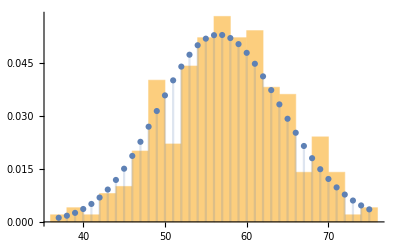

```mathematica
lengths=Length/@lums;
poissonDist=EstimatedDistribution[lengths,PoissonDistribution[λ]]
Show[Histogram[lengths,"Knuth","PDF"],DiscretePlot[PDF[poissonDist,Ni],{Ni,Min[lengths],Max[lengths]}]]
```

```mathematica
replicaDist=SmoothKernelDistribution[lumSum,"Scott","Gaussian"];
{Mean[lumSum],StandardDeviation[lumSum]}
%[[2]]/%[[1]]
NMaximize[{PDF[replicaDist,l],l≥ Min[lumSum]&&l≤ Max[lumSum]},{l},Method->"SimulatedAnnealing"]
Show[Histogram[lumSum,20,"PDF"],Plot[PDF[replicaDist,l],{l,Min[lumSum],Max[lumSum]}] ]
```

SmoothKernelDistribution::rctn: A rectangular array of real numbers is expected at position 1 in SmoothKernelDistribution[lumSum].

{Mean[lumSum],StandardDeviation[lumSum]}

StandardDeviation[lumSum]/Mean[lumSum]

NMaximize::bcons: The following constraints are not valid: {l ≥ lumSum, l ≤ lumSum}. Constraints should be equalities, inequalities, or domain specifications involving the variables.

NMaximize[{PDF[SmoothKernelDistribution[lumSum,Scott,Gaussian],l],l≥lumSum&&l≤lumSum},{l},Method→SimulatedAnnealing]

Histogram::ldata: lumSum is not a valid dataset or list of datasets.

Plot::plln: Limiting value lumSum in {l, Min[lumSum], Max[lumSum]} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[Histogram[lumSum, 20, "PDF"], Plot[PDF[replicaDist, l], {l, Min[lumSum], Max[lumSum]}]].

Show[Histogram[lumSum,20,PDF],Plot[PDF[replicaDist,l],{l,Min[lumSum],Max[lumSum]}]]

```mathematica
binData=Cases[data,binSpec];
Dimensions[binData]
```

{59,2}

## Compare Poisson posterior predictive to distribution of packets across simulations

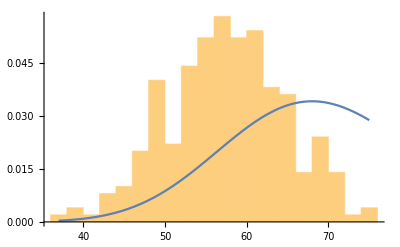

```mathematica
PNgivenn[Ni_,ni_]:=Pochhammer[Ni+ni+1,Ni+ni]/(Pochhammer[ni+1,ni] 2^(3Ni+ni+1/2)Ni!)
Show[Histogram[lengths,"Knuth","PDF"],
Plot[PNgivenn[Ni,lengths[[run-2]]],{Ni,Min[lengths],Max[lengths]}]
]
```

```mathematica
N[Log[Apply[PNgivenn,#]]]&/@{{13, 11},{11,13},{1,2}}
```

{-2.63578,-2.554,-1.50972}

## Estimate distribution P(L|θ) from a single run for one bin First guess yields a ‘hedgehog’ plot with variance of by a factor of 2.

```mathematica
empiricalDist[Ni_,luminosities_]:=Module[{sums},
sums=Take[ListConvolve[Table[1,{i,Ni}],luminosities],{1,-1,Ni}]; (* uncorrelated *)
SmoothKernelDistribution[sums,"Oversmooth","Gaussian"]
]

Needs["MyBinarySearch`"];

PLgivenθ1[Li_,sortedPairs_,νmin_:1.5 10^15,binwidth_:3.925828717905795 10^12]:=Module[{imin,imax,iMultiMin, iMultiMax, ni,li,dist,nMultiBin=3000},

(* index of first element in frequency bin *)
imin=binSearchMin[sortedPairs[[;;,1]], νmin];
imax=binSearchMax[sortedPairs[[;;,1]], νmin+binwidth];
li=Total[sortedPairs[[imin;;imax,2]]];
ni=imax-imin+1;
(*Print[{imin,imax,li}];*)

(* get elements in vicinity *)
(* TODO handle border cases *)
If[ni≥ nMultiBin,
iMultiMin=imin;iMultiMax=imax,

(* half of elements added on either side of bin *)
iMultiMin=imin-Floor[(nMultiBin-ni)/2];
iMultiMax=imax+Floor[(nMultiBin-ni)/2];
];
(*Print[{iMultiMax,iMultiMin}];*)
(*Print[Dimensions[sortedPairs[[iMultiMin;;iMultiMax,2]]]];*)
Sum[
(*NIntegrate[*)
PDF[empiricalDist[Ni,sortedPairs[[iMultiMin;;iMultiMax,2]]],Li] PNgivenn[Ni,ni],{Ni,Max[0,ni-3Floor[√ni]],Min[Length[sortedPairs],ni+3Floor[√ni]]}]

]
(*Plot[PDF[empiricalDist[72,sortedData[[67655;;68654,2]]],Li],{Li,1 10^40,1.1 10^40}]*)
Plot[PLgivenθ1[Li,sortedData,1.1998 10^15,0.0002 10^15],{Li,0.5 10^39,3 10^39}]
```

-Graphics-

```mathematica
Lθ1=Apply[WeightedData,Transpose[Table[{Li,PLgivenθ1[Li,sortedData,1.198 10^15,0.002 10^15]},{Li,1.45 10^40,1.85 10^40,0.025 10^40}]]]
```

WeightedData[…]

Std. dev. only 50% of what it should be

```mathematica
StandardDeviation[Lθ1]
```

1.20329×10^39

## Next approach to estimate P(L|θ). Use central limit theorem because there are many packets in the bin the bootstrap doesn’t do well because there are only 10 samples or so to estimate the pdf by KDE.

```mathematica
PLgivenθ2[Li_,sortedPairs_,νmin_:1.5 10^15,binwidth_:3.925828717905795 10^12]:=Module[{imin,imax,iMultiMin, iMultiMax, ni,li,dist,nMultiBin=3000,mean,var},

(* index of first element in frequency bin *)
imin=binSearchMin[sortedPairs[[;;,1]], νmin];
imax=binSearchMax[sortedPairs[[;;,1]], νmin+binwidth]-1;
li=Total[sortedPairs[[imin;;imax,2]]];
ni=imax-imin+1;
Print[{imin,imax,li}];
Print[{imin,sortedPairs[[imin]]}];
Print[{imax,sortedPairs[[imax]]}];

(* get elements in vicinity *)
(* TODO handle border cases *)
If[ni≥ nMultiBin,
iMultiMin=imin;iMultiMax=imax,

(* half of elements added on either side of bin *)
iMultiMin=imin-Floor[(nMultiBin-ni)/2];
iMultiMax=imax+Floor[(nMultiBin-ni)/2];
];

(* compute mean and variance for CLT *)
mean=Mean[sortedPairs[[iMultiMin;;iMultiMax,2]]];
var=Variance[sortedPairs[[iMultiMin;;iMultiMax,2]]];
(*Print[{Moment[(sortedPairs[[iMultiMin;;iMultiMax,2]]-mean)/stddev,3], Moment[(sortedPairs[[iMultiMin;;iMultiMax,2]]-mean)/stddev,4]}];
*)(*Print[{mean,stddev}];*)
(*Print[{iMultiMax,iMultiMin}];*)
(*Print[Dimensions[sortedPairs[[iMultiMin;;iMultiMax,2]]]];*)
Print[ N[PNgivenn[ni,ni]];PDF[NormalDistribution[ni mean,Sqrt[ni var]],Li]];
(*NIntegrate[*)
Sum[
PDF[NormalDistribution[Ni mean,√(Ni var)],Li] PNgivenn[Ni,ni],

{Ni,Max[0,ni-2Floor[√ni]],Min[Length[sortedPairs],ni+2Floor[√ni]]}
]

]
With[{ν1=1.1998 10^15,binwidth=0.0002 10^15,Lmin=0.5 10^39,Lmax=4 10^39,ΔL=0.5 10^39},
Print[PLgivenθ2[1.66565 10^39,sortedData,ν1,binwidth]];
(*Lθ2=Apply[WeightedData,Transpose[Table[{Li,PLgivenθ2[Li,sortedData,ν1,binwidth]},{Li,Lmin,Lmax,ΔL}]]];
Print[StandardDeviation[Lθ2]];
temp=StringTemplate["`1`, σ=`2`e39"];
dist=SmoothKernelDistribution[Lθ2];
Export["PL.pdf",
Plot[{PDF[SmoothKernelDistribution[Lθ2],Li],PDF[replicaDist,Li]},{Li,Min[lumSum],Max[lumSum]},
PlotLegends->{temp["single run",10^-39 StandardDeviation[dist]],temp[ "250 runs",10^-39 StandardDeviation[replicaDist]]},
PlotLabel->"P(L|θ)",
Frame->True,FrameLabel->"L for ν ∈ [1.198,1.2]x10^15"
]
]*)
]
```

{60022,60033,1.66565×10^39}

{60022,{1.1998×10^15,1.38329×10^38}}

{60033,{1.19998×10^15,1.44311×10^38}}

1.22802×10^-38

9.9483×10^-40

## Why uncertainty underestimated? Poisson seems fine. Either CLT variance too small or I forgot something in my derivation. Didn’t include enough terms in the sum over N_i

## Edgeworth expansion to get asymmetric corrections to Gaussian for CLT. => It can easily get negative depending on γ, the third moment

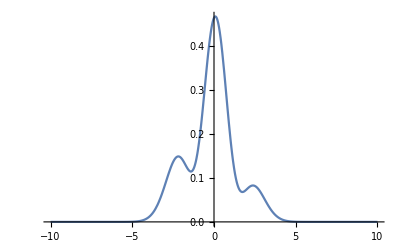

```mathematica
Module[{μ=0,σ=1,γ=-1.12024+0.9,τ=4.8,n=5},

g[x_]:=PDF[NormalDistribution[μ,σ],x](1+(γ HermiteH[3,x])/(6 √n)+((τ-3)HermiteH[4,x])/(24 n)+(γ^2 HermiteH[6,x])/(72n));
Plot[g[x],{x,-10,10}]
]
```